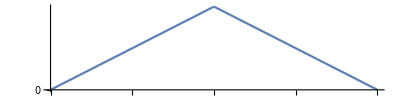

0.5+(-1)**floor(X/8)*(-0.5+1.*np.mod(X/8,1))

```mathematica
T=64;OO=4;
(*T=TTTT;OO=OOOO;*)
ᐱ[X_]:=(T*(0.5+(-1)^Floor[(2*OO*X)/T]*(-0.5+Mod[(2*OO*X)/T,1])))/64;
Plot[
ᐱ[X]
,
{X,0,16},AspectRatio->1/4,ImageSize->Full,Ticks->{Range[0,16,4],Range[0,16,1]}]
StringReplace[ToLowerCase[ToString[FullSimplify[ExpandAll[ᐱ[X]]],InputForm]],{"["-> "(","]"-> ")","^"-> "**","oooo"-> "O","tt"-> "T","x"-> "X"," "-> "","mod"-> "np.mod","i"-> "sqrt(-1)","pi"-> "4*atan(1)"}]
```

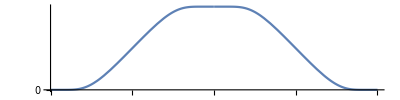

0.5-0.5*(-1)**floor(X/8)+(-1)**floor(X/8)/(1+e**(8*((-8+np.mod(X,8))**(-1)+np.mod(X,8)**(-1))))

```mathematica
T=64;OO=4;
(*T=TTTT;OO=OOOO;*)
Θ[X_]=Exp[-(T/2/OO)/X]/(Exp[-(T/2/OO)/X]+Exp[-(T/2/OO)/((T/2/OO)-X)]);
ƎE[X_]=(-1)^Floor[X/(T/2/OO)]*(Θ[Mod[X,(T/2/OO)]]-.5)+.5;
Plot[
ƎE[X]
,
{X,0,16},AspectRatio->1/4,ImageSize->Full,Ticks->{Range[0,16,4],Range[0,16,1]}]
StringReplace[ToLowerCase[ToString[FullSimplify[ExpandAll[ƎE[X]]],InputForm]],{"["-> "(","]"-> ")","^"-> "**","oooo"-> "O","tt"-> "T","x"-> "X"," "-> "","mod"-> "np.mod","i"-> "sqrt(-1)","pi"-> "4*atan(1)"}]
```